### open MATLAB

```mathematica
SetEnvironment["PATH"->"D:\\Wolfram_Mathematica_12\\SystemFiles\\Libraries\\Windows-x86-64;D:\\Wolfram_Mathematica_12\\SystemFiles\\Libraries\\Windows;D:\\Wolfram_Mathematica_12\\SystemFiles\\Kernel\\Binaries\\Windows-x86-64;D:\\Wolfram_Mathematica_12;D:\\Wolfram_Mathematica_12\\SystemFiles\\FrontEnd\\Binaries\\Windows-x86-64;D:\\Wolfram_Mathematica_12\\SystemFiles\\Kernel\\Binaries\\Windows-x86-64;C:\\Program Files\\Rtools\\bin;C:\\Program Files (x86)\\Common Files\\Oracle\\Java\\javapath;C:\\ProgramData\\Oracle\\Java\\javapath;C:\\Program Files (x86)\\PHP\\v7.0;C:\\Program Files (x86)\\Google\\Chrome\\Application;C:\\Program Files (x86)\\Intel\\iCLS Client\\;C:\\Program Files\\Intel\\iCLS Client\\;C:\\Windows\\system32;C:\\Windows;C:\\Windows\\System32\\Wbem;C:\\Windows\\System32\\WindowsPowerShell\\v1.0\\;C:\\windows\\syswow64;C:\\Program Files (x86)\\Novell\\ZENworks\\bin;C:\\Program Files (x86)\\Intel\\Intel(R) Management Engine Components\\DAL;C:\\Program Files\\Intel\\Intel(R) Management Engine Components\\DAL;C:\\Program Files (x86)\\Intel\\Intel(R) Management Engine Components\\IPT;C:\\Program Files\\Intel\\Intel(R) Management Engine Components\\IPT;C:\\Program Files\\Novell\\iPrint;C:\\Program Files\\MATLAB\\R2020a\\bin;C:\\Program Files\\MATLAB\\R2014a\\bin;Z:.;C:\\Program Files (x86)\\Wolfram Research\\WolframScript\\;C:\\Program Files\\Microsoft VS Code\\bin;C:\\Users\\Administrator\\AppData\\Local\\Programs\\Python\\Python38-32\\Scripts\\;C:\\Users\\Administrator\\AppData\\Local\\Programs\\Python\\Python38-32\\;Z:.;C:\\Program Files\\MATLAB\\R2020a\\bin\\win64;" ];
```

```mathematica
Needs["MATLink`"]
```

```mathematica
OpenMATLAB[]
```

### utca-poligonokkal - leegyszerűsített

```mathematica
Manipulate[
Plot[
1/(1+Exp[graduality (x-halfStrengthPoint totalWidth/2)])-1/(1+Exp[graduality (totalWidth/2-halfStrengthPoint  totalWidth/2)])
,{x,0,totalWidth},PlotRange->{{0,totalWidth/2},{0,1}}],
{{graduality,0.1},0,2,10^-3},
{{halfStrengthPoint,0.5},0,1,10^-3}]
```

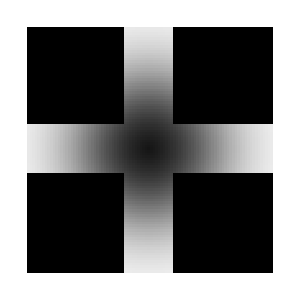
-Graphics--Graphics-

```mathematica
halfStrengthPoint=0.5;
graduality=0.1;
totalWidth=Round[shrink gS (sW+bW)];
streetWidth=Round[sW shrink gS];
illusionMatrix=Table[Table[
If[
-0.5streetWidth<l-0.5totalWidth<0.5streetWidth||-0.5streetWidth<k-0.5totalWidth<0.5streetWidth ,
1/(1+Exp[graduality (EuclideanDistance[{0,0},{k,l}-0.5totalWidth]-halfStrengthPoint 0.5 totalWidth)]),
-1
]
,{l,1,totalWidth}],{k,1,totalWidth}];
Row[{
ArrayPlot[illusionMatrix,ImageSize->{300,300}],
MatrixPlot[illusionMatrix,PlotLegends->True,FrameTicks->None,ImageSize->{300,300}]}]
```

```mathematica
MEvaluate["clear all"];
MEvaluate["illusionMatrix = generateIllusionMatrix("<>ToString[totalWidth]<>","<>ToString[streetWidth]<>",0.1,0.5);"];
illusionMatrixMATLAB = MGet["illusionMatrix"];
Row[{
ArrayPlot[illusionMatrixMATLAB,ImageSize->{300,300}],
MatrixPlot[illusionMatrixMATLAB,PlotLegends->True,FrameTicks->None,ImageSize->{300,300}]}]
```

-Graphics--Graphics-

```mathematica
n=5;r=0.25;gS=500;gC={250,250};

sW=(r/(1+r))(1/n); 
bW=(1/(1+r)) (1/n);
shrink=1/((n+1)sW+n bW);

coords=Table[sW (i-1)+bW (i-1)-0.5,{i,1,n+1}];

verticalStreets =Table[gS shrink{
{coords[[i]],-0.5}+ sW/2{1,1},
{coords[[i]],-0.5}+ sW/2{-1,1},
{coords[[i]],0.5}+ sW/2{-1,1},
{coords[[i]],0.5}+ sW/2{1,1}
},{i,1,n+1}];
horizontalStreets =Table[gS shrink{
{-0.5,coords[[i]]}+sW/2{-1,-1},
{-0.5,coords[[i]]}+sW/2{-1,1},
{0.5,coords[[i]]}+sW/2{1,1},
{0.5,coords[[i]]}+sW/2{1,-1}
},{i,1,n+1}];

crossings = Table[Table[gS shrink{coords[[i]],coords[[j]]}+gC,{j,1,n+1}],{i,1,n+1}];

halfStrengthPoint=0.5;
graduality=0.05;
illusionSize=shrink gS (sW+bW);
illusionMatrix=Table[Table[
If[
-0.5sW shrink gS<l<0.5sW shrink gS ||-0.5sW shrink gS<k<0.5sW shrink gS ,
1/(1+Exp[graduality (EuclideanDistance[{0,0},{k,l}]-halfStrengthPoint 0.5 illusionSize)]),
0.5
]
,{l,-0.5illusionSize,0.5illusionSize}],{k,-0.5illusionSize,0.5illusionSize}];

gridPoints=Map[Map[#+gC&,#]&,Join[horizontalStreets,verticalStreets]];
```

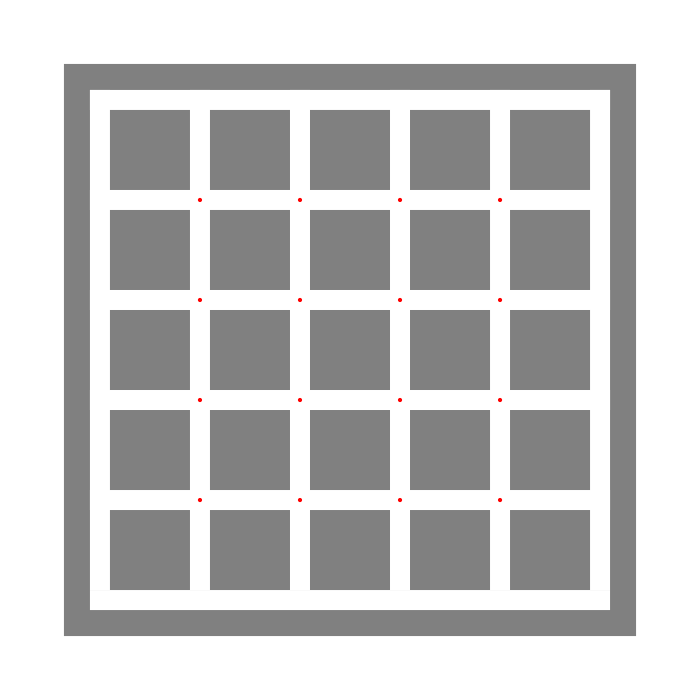

```mathematica
Graphics[{
Gray,EdgeForm[None],Rectangle[gC-1.1gS/2,gC+1.1gS/2],
White,Map[Polygon,gridPoints],
RGBColor[0,0,0,0],
EdgeForm[{Green,Thickness [0.0025]}],Rectangle[{-0.5,-0.5},{0.5,0.5}],
EdgeForm[{Red,Thickness [0.0025]}],Rectangle[gC-gS/2,gC+gS/2],
RGBColor[1,0,0,1],
Table[Table[
Point[crossings[[i]][[j]]]
,{j,2,n}],{i,2,n}]
},ImageSize->{700,700},AspectRatio->1]
```

```mathematica
MEvaluate["addpath('Y:/Beno/hermann_grid')"]
```

```mathematica
MEvaluate["[gridElements, crossings, illusionMatrix] = generateGrid([250 250], 500, 5, 0.25, 0.1, 0.5);"];
gridPointsMATLAB=MGet["gridElements"];
crossingsMATLAB = MGet["crossings"];
illusionMatrixMATLAB = MGet["illusionMatrix"];
```

```mathematica
Graphics[{
Gray,EdgeForm[None],Rectangle[gC-1.1gS/2,gC+1.1gS/2],
White,Map[Polygon,gridPointsMATLAB],
RGBColor[0,0,0,0],
EdgeForm[{Green,Thickness [0.0025]}],Rectangle[{-0.5,-0.5},{0.5,0.5}],
EdgeForm[{Red,Thickness [0.0025]}],Rectangle[gC-gS/2,gC+gS/2],
RGBColor[1,0,0,1],
Table[Table[
Point[crossingsMATLAB[[i]][[j]]]
,{j,2,n}],{i,2,n}]
},ImageSize->{700,700},AspectRatio->1]
```

-Graphics-

```mathematica
1/3 {a,b,c}.{1,1,1}
```

1/3 (a+b+c)

### utca-poligonokkal

```mathematica
n=5; res=100; r=0.25;
sNL=0.5; bNL=0.5;
sC={0.5,0.5}; sL=2; sS=10; sA=0.0;
scintillation=True; aperture = False;
aC={0.5,0.5}; aW=1.1; aO = 0.85;
sW=(r/(1+r))(1/n); bW=(1/(1+r)) (1/n);

sNH=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];
bNH=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];
sNV=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];
bNV=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];

hCoords=Table[
(sW Total[sNH[[1;;i-1]]]+bW Total[bNH[[1;;i-1]]]+sW(sNH[[i]]-sNH[[1]])/2)/
(sW Total[sNH]+bW Total[bNH]-sW(sNH[[1]]+sNH[[n]])/2)
,{i,1,n+1}];

vCoords=Table[
(sW Total[sNV[[1;;i-1]]]+bW Total[bNV[[1;;i-1]]]+sW(sNV[[i]]-sNV[[1]])/2)/
(sW Total[sNV]+bW Total[bNV]-sW(sNV[[1]]+sNV[[n]])/2)
,{i,1,n+1}];

hWidthComponents =Table[sW sNH[[i]],{i,1,n+1}];
vWidthComponents =Table[sW sNV[[i]],{i,1,n+1}];
```

```mathematica
SinFunction[k_]:=sA bW Sin[2 Pi k n]
PatchFunction[h_,v_]:=(1/(1+Exp[sS (2EuclideanDistance[sC,{h,v}]-sL)]))

verticalStreets=Table[
Map[#+{hCoords[[i]],0.5}&,Map[#-{hCoords[[i]],0.5}&,Join[
Table[
{hCoords[[i]]+0.5hWidthComponents[[i]]+SinFunction[k]PatchFunction[hCoords[[i]]+0.5hWidthComponents[[i]],k],k}
,{k,0,1,1/res}],
Reverse[Table[
{hCoords[[i]]-0.5hWidthComponents[[i]]+SinFunction[k]PatchFunction[hCoords[[i]]-0.5hWidthComponents[[i]],k],k}
,{k,0,1,1/res}]]
]]],
{i,1,n+1}] ;

horizontalStreets=
Table[
Map[#+{0.5,vCoords[[i]]}&,Map[#-{0.5,vCoords[[i]]}&,Join[
Table[
{k,vCoords[[i]]+0.5vWidthComponents[[i]]-SinFunction[k]PatchFunction[k,vCoords[[i]]+0.5vWidthComponents[[i]]]}
,{k,0,1,1/res}],
Reverse[Table[
{k,vCoords[[i]]-0.5vWidthComponents[[i]]-SinFunction[k]PatchFunction[k,vCoords[[i]]-0.5vWidthComponents[[i]]]}
,{k,0,1,1/res}]]
]]],
{i,1,n+1}];

aperturePoints=Map[
aC+ aW #&,
Join[
Table[(aO/2){Cos[k],Sin[k]},{k,0,2Pi,Pi/100}],
{{0.5,0},{0.5,-0.5},{-0.5,-0.5},{-0.5,0.5},{0.5,0.5},{0.5,0},{0.5,0}}
]
];

hShift=(Max[horizontalStreets]-1-Abs[Min[horizontalStreets]])/2;
vShift=(Max[verticalStreets]-1-Abs[Min[verticalStreets]])/2;

shrink=1/Max[Max[horizontalStreets]-Min[horizontalStreets]-hShift,Max[verticalStreets]-Min[verticalStreets]-hShift];
shrink=1;

crossings =Table[Table[
If[
i≠1&&j≠1&&i≠n+1&&j≠n+1,
shrink{ hCoords[[i]]-vShift-0.5,vCoords[[j]]-hShift-0.5},
{0,0}
]
,{j,1,n+1}],{i,1,n+1}];

gridPoints=
shrink Join[
Map[Map[#+{-0.5,-0.5}&,#]&,horizontalStreets-hShift],
Map[Map[#+{-0.5,-0.5}&,#]&,verticalStreets-vShift]
];
```

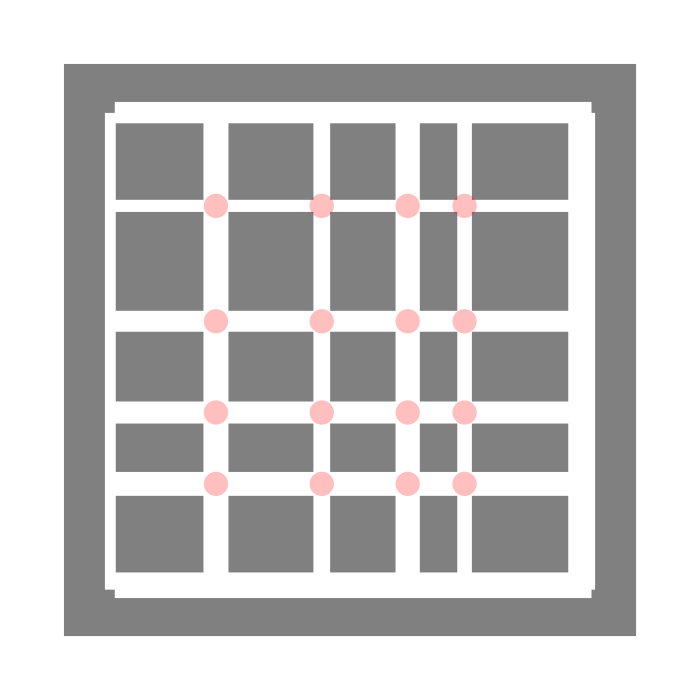

```mathematica
Graphics[{
Gray,Rectangle[{-0.6,-0.6},{0.6,0.6}],
White,Map[Polygon,gridPoints],
RGBColor[0,0,0,0],
EdgeForm[{Green,Thickness [0.0025]}],Rectangle[{-0.5,-0.5},{0.5,0.5}],
Table[Table[{
PointSize->0.025,RGBColor[1,0,0,0.25],
Point[crossings[[j]][[i]]]
}
,{j,2,n}],{i,2,n}],
RGBColor[1,0,0,1],Thick
},ImageSize->{700,700},AspectRatio->1]
```

```mathematica
shrink (Total[sNH sW]+Total[bNH bW])
```

1.15334

```mathematica
shrink (Total[sNV sW]+Total[bNV bW])
```

1.1628

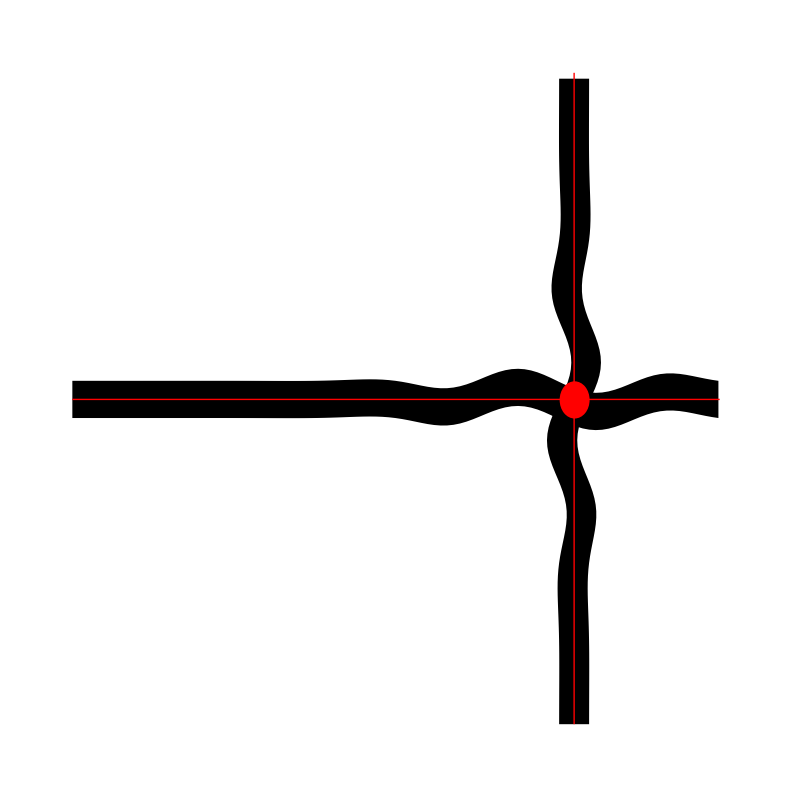

```mathematica
h=4;
v=4;
Graphics[{
Polygon[gridPoints[[h]]],
Polygon[gridPoints[[n+v]]],
Red,Ellipsoid[{hCoords[[h]],vCoords[[v-1]]},0.5{sW sNH[[h]],sW sNV[[v-1]]}],
Line[{{hCoords[[h]],Max[hCoords]},{hCoords[[h]],Min[hCoords]}}],
Line[{{Min[vCoords],vCoords[[v-1]]},{Max[vCoords],vCoords[[v-1]]}}]
}]
```

```mathematica
Export["Y:\\Beno\\hermann_grid\\grids\\16_sine_patchy_with_aperture.png",gridGraphic,ImageResolution->200]
```

Y:\Beno\hermann_grid\grids\16_sine_patchy_with_aperture.png

```mathematica
Table[k,{k,0,2 Pi,Pi/100}]//Last
```

2 π

```mathematica
OpenMATLAB[]
```

```mathematica
MEvaluate["addpath('Y:/Beno/hermann_grid/')"]
```

```mathematica
n=4;
gS=1;
```

```mathematica
MEvaluate["clear all"];
MEvaluate["[gridElements, scintillationPoints, apertureElement, crossings, debug] = generateGrid([0 0], 1, 4, 0.5, 0.5, 0.5, [0.5, 0.5], 2, 10, 0.0, [0.5, 0.5], 1.5, 0.5)"];
(*generateGrid(    gC,       gS, n,  r,   sNL, bNL,     sC,     sL, sS, sA,      aC,     aS,  aO )*) 
gridPoints=MGet["gridElements"];
scintillationPoints=MGet["scintillationPoints"];
crossings=MGet["crossings"];
debug=MGet["debug"];
bNH=debug[[1]];
bNV=debug[[2]];
sNH=debug[[3]];
sNV=debug[[4]];
bW=debug[[5]];
sW=debug[[6]];
shrink=debug[[7]];
hShift=debug[[8]];
vShift=debug[[9]];
```

```mathematica
crossings//Dimensions
```

{25,4,2}

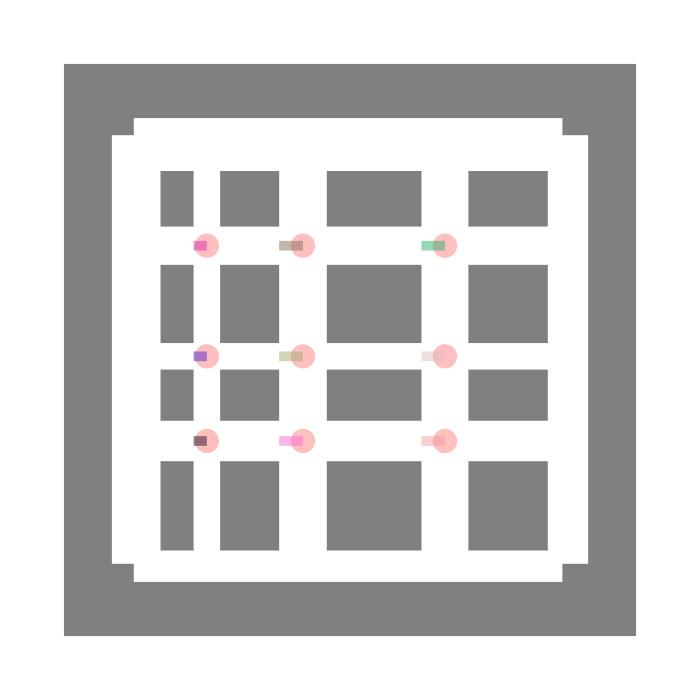

```mathematica
Graphics[{
Gray,Rectangle[{-0.6,-0.6},{0.6,0.6}],
White,Map[Polygon,gridPoints],
RGBColor[0,0,0,0],
EdgeForm[{Green,Thickness [0.0025]}],Rectangle[{-0.5,-0.5},{0.5,0.5}],
EdgeForm[None],
Table[Table[{
PointSize->0.025,RGBColor[1,0,0,0.25],
Point[crossings[[j+(i-1)(n+1)]][[1]]],
Thickness->0.01,CapForm->None,
RGBColor[RandomReal[],RandomReal[],RandomReal[],0.5],
Line[{
crossings[[j+(i-1)(n+1)]][[1]]-gS shrink{0bNH[[i-1]]bW+0.5sNH[[i]]sW,0},
crossings[[j+(i-1)(n+1)]][[1]]
}]
}
,{j,2,n}],{i,2,n}]
},ImageSize->{700,700},AspectRatio->1]
```

```mathematica
shrink Total[sNH sW]+Total[bNH bW]
```

1.1018

```mathematica
shrink Total[sNV sW]+Total[bNV bW]
```

1.0932

```mathematica
bW
```

0.166667

```mathematica
bNH
```

{0.502238,0.879724,1.40441,1.18035}

```mathematica
1/shrink
```

1.05943

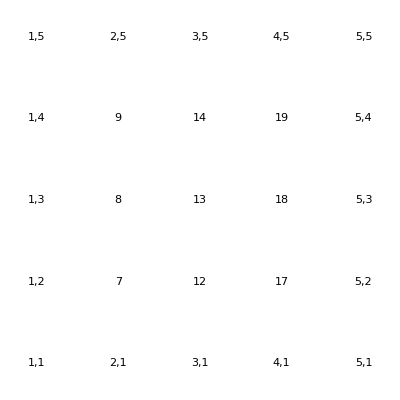

```mathematica
Graphics[
Table[Table[
Text[
If[
i≠1&&j≠1&&i≠n+1&&j≠n+1,
ToString[j+(i-1)(n+1)],
ToString[i]<>","<>ToString[j]
]
,{i,j}]
,{j,1,n+1}],{i,1,n+1}]
]
```

### animálás

```mathematica
GridGenerator[n_,r_,sNL_,bNL_,sC_,sL_,sS_,sA_,aperture_,aC_,aW_,aO_,s_,parameters_]:=Module[
{res,sW,bW,sNH,bNH,sNV,bNV,aperturePoints,hCoords,vCoords,gridPoints,gridGraphic},
res=100;
sW=(r/(1+r))(1/n);
bW=(1/(1+r)) (1/n);
sNH=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];
bNH=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];
sNV=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];
bNV=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];

aperturePoints=Map[
aC+ aW #&,
Join[
Table[(aO/2){Cos[k],Sin[k]},{k,0,2Pi,Pi/100}],
{{0.5,0},{0.5,-0.5},{-0.5,-0.5},{-0.5,0.5},{0.5,0.5},{0.5,0},{0.5,0}}
]
];

hCoords=Table[
(sW Total[sNH[[1;;i-1]]]+bW Total[bNH[[1;;i-1]]]+sW(sNH[[i]]-sNH[[1]])/2)/
(sW Total[sNH]+bW Total[bNH]-sW(sNH[[1]]+sNH[[n]])/2)
,{i,1,n+1}];
vCoords=Table[
(sW Total[sNV[[1;;i-1]]]+bW Total[bNV[[1;;i-1]]]+sW(sNV[[i]]-sNV[[1]])/2)/
(sW Total[sNV]+bW Total[bNV]-sW(sNV[[1]]+sNV[[n]])/2)
,{i,1,n+1}];

gridPoints=Join[
Table[Join[
Table[
{
hCoords[[i]]+0.5sW sNH[[i]]+
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{hCoords[[i]]+0.5sW sNH[[i]],k}]-sL)])),
k
}
,{k,0,1,1/res}],
Reverse[Table[
{
hCoords[[i]]-0.5sW sNH[[i]]+
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{hCoords[[i]]-0.5sW sNH[[i]],k}]-sL)])),
k
}
,{k,0,1,1/res}]]
],
{i,1,n+1}],
Table[Join[
Table[
{
k,
vCoords[[i]]+0.5sW sNV[[i]]-
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{k,vCoords[[i]]+0.5sW sNV[[i]]}]-sL)]))
}
,{k,0,1,1/res}],
Reverse[Table[
{
k,
vCoords[[i]]-0.5sW sNV[[i]]-
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{k,vCoords[[i]]-0.5sW sNV[[i]]}]-sL)]))
}
,{k,0,1,1/res}]]
],
{i,1,n+1}]
];

gridGraphic=ArrayReshape[Join[
{
Graphics[{FontFamily->"Cambria",FontSize->18,
Text[
"number of blocks = "<>ToString[n]<>", street/block ratio = "<>ToString[r]<>"\nstreet noise = ±"<>ToString[sNL]<>", block noise = ±"<>ToString[bNL]<>", "<>"\nsine amplitude = "<>ToString[sA]<>", sine cutoff = "<>If[sA==0||1<sL,"0",ToString[sS]]
,{0.5,1.075}]
},ImageSize->{s,100},AspectRatio->0.025],
Graphics[ImageSize->{700,100},AspectRatio->0.025]
},
Table[
Graphics[{
Black,EdgeForm[Gray],Rectangle[{0,0},{1,1}],
EdgeForm[None],
If[
scintillation,
{
RGBColor[0.5,0.5,0.5,1],Map[Polygon,gridPoints],
RGBColor[1,1,1],Table[Table[
Ellipsoid[{hCoords[[i]],vCoords[[j]]},0.5{sW sNH[[i]],sW sNV[[j]]}]
,{j,1,n+1}],{i,1,n+1}]
},
{
White,Map[Polygon,gridPoints]
}
],
If[
aperture,
{
RGBColor[0.5,0.5,0.5,0.99],Polygon[aperturePoints]
}
]
},ImageSize->{s,s},AspectRatio->1],{scintillation,{False,True}}]
],{2,2}];

If[parameters,Grid[gridGraphic],Row[gridGraphic[[2]]]]
]
```

n,      r,   sNL, bNL,     sC,             sL,    sS ,   sA ,aperture ,      aC ,        aW ,aO,    s

```mathematica
tRes=100;
frames=Table[
GridGenerator[11,0.25,0,0,{0.5,0.5}+0.25{Cos[2Pi t],Sin[2Pi t]},0.3,10,0.1,False,{0.5,0.5},1,0.5,400,False]
,{t,0,1,1/(tRes-1)}];
```

```mathematica
Export["Y:\\Beno\\hermann_grid\\grids\\anim\\test.gif",frames]
```

Y:\Beno\hermann_grid\grids\anim\test.gif

```mathematica
tRes=100;
AnimatorFunction[t_]:=Piecewise[{
{Power[1.5t(1-1.5t)/0.25,3],t<1/3},
{1,1/3≤t≤2/3},
{Power[1.5(t-1/3)(1-1.5(t-1/3))/0.25,3],2/3<t}
}];
AnimatorFunction[t_]:=4t(1-t)
frames=Table[
GridGenerator[7,0.25,0,0,{0.5,0.5},0.75AnimatorFunction[t],10,0.1,False,{0.5,0.5},1,0.5,400,False]
,{t,0,1,1/(tRes-1)}];
```

```mathematica
Export["Y:\\Beno\\hermann_grid\\grids\\anim\\sine_growing_patch.gif",frames]
```

Y:\Beno\hermann_grid\grids\anim\sine_growing_patch.gif

```mathematica
ListAnimate[frames]
```

### MATLAB

```mathematica
{sNH,bNH,sNV,bNV}=Map[First,Import["Y:\\Beno\\hermann_grid\\noise_parameters.mat"][[1]][[1]]];
{hCoordsMATLAB,vCoordsMATLAB}=Map[First,Import["Y:\\Beno\\hermann_grid\\coords.mat"][[1]][[1]]];
n=2;
res=100;
r=0.25;

sC={0.75,0.5};
sL=0.4;
sS=10;
sA=0;

sW=(r/(1+r))(1/n);
bW=(1/(1+r)) (1/n);

hCoords=Table[
(
sW Total[sNH[[1;;i-1]]]+
bW Total[bNH[[1;;i-1]]]+
sW(sNH[[i]]-sNH[[1]])/2
)/(
sW Total[sNH]+
bW Total[bNH]-
sW(sNH[[1]]+sNH[[n]])/2
)
,{i,1,n+1}];
vCoords=Table[
(sW Total[sNV[[1;;i-1]]]+bW Total[bNV[[1;;i-1]]]+sW(sNV[[i]]-sNV[[1]])/2)/
(sW Total[sNV]+bW Total[bNV]-sW(sNV[[1]]+sNV[[n]])/2)
,{i,1,n+1}];

gridMathematica=Join[
Table[
Join[
Table[
{
hCoords[[i]]+0.5sW sNH[[i]]+
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{hCoords[[i]]+0.5sW sNH[[i]],k}]-sL)])),
k
}
,{k,0,1,1/res}],
Reverse[Table[
{
hCoords[[i]]-0.5sW sNH[[i]]+
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{hCoords[[i]]-0.5sW sNH[[i]],k}]-sL)])),
k
}
,{k,0,1,1/res}]]
],
{i,1,n+1}],
Table[
Join[
Table[
{
k,
vCoords[[i]]+0.5sW sNV[[i]]-
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{k,vCoords[[i]]+0.5sW sNV[[i]]}]-sL)]))
}
,{k,0,1,1/res}],
Reverse[Table[
{
k,
vCoords[[i]]-0.5sW sNV[[i]]-
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{k,vCoords[[i]]-0.5sW sNV[[i]]}]-sL)]))
}
,{k,0,1,1/res}]]
],
{i,1,n+1}]
];
gridMATLAB=Map[Transpose,Import["Y:\\Beno\\hermann_grid\\grid.mat"][[1]][[1]]];
```

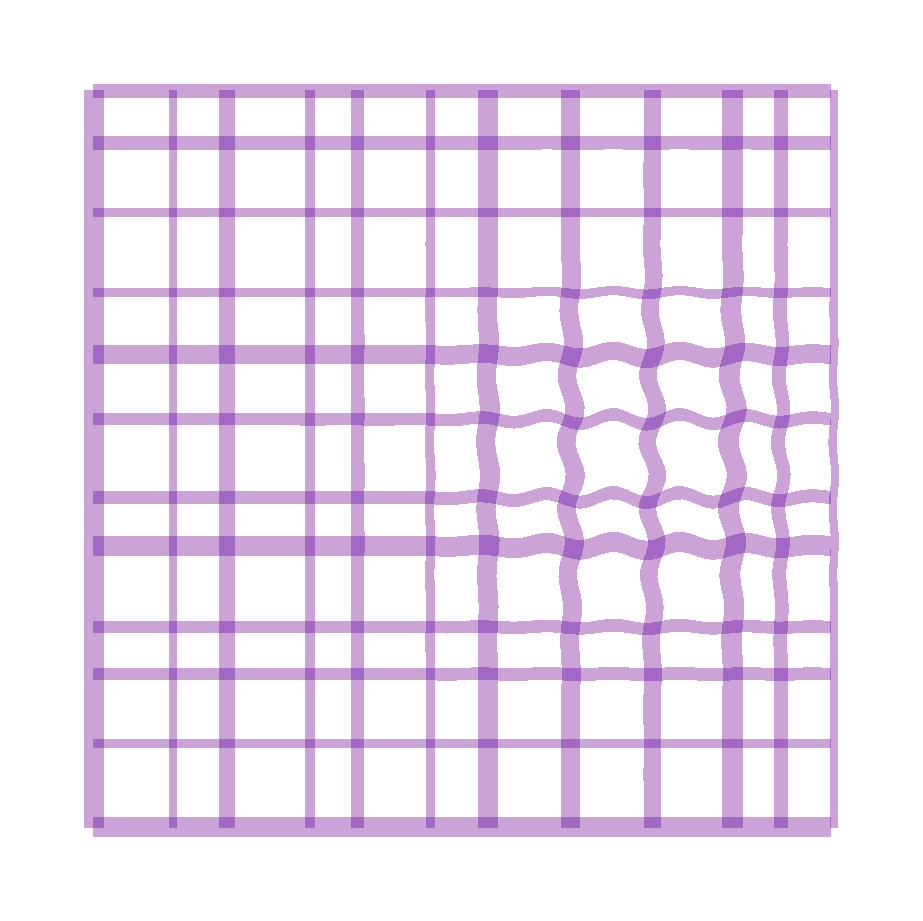

```mathematica
i=2;
Graphics[{
RGBColor[1,0,0,0.2],Map[Polygon,gridMathematica],
RGBColor[0,0,1,0.2],Map[Polygon,gridMATLAB]
}]
```

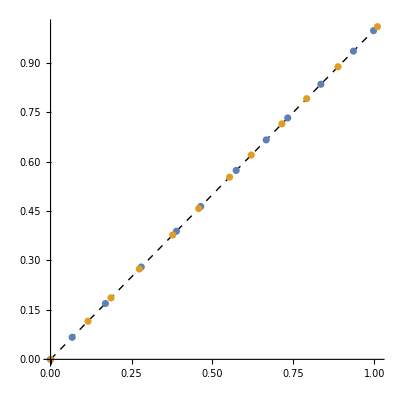

```mathematica
ListPlot[
{
Transpose[{hCoords,hCoordsMATLAB}],
Transpose[{vCoords,vCoordsMATLAB}]
},AspectRatio->1,Prolog->{Black,Dashed,Thin,Line[{{0,0},{1,1}}]}]
```

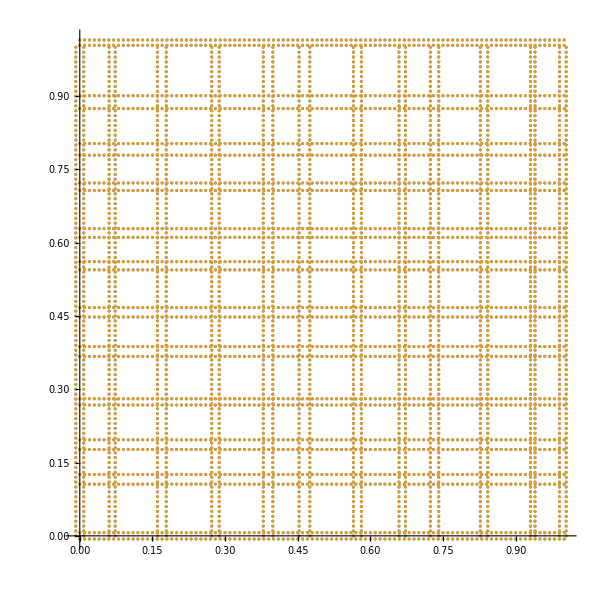

```mathematica
ListPlot[
{
Flatten[gridMathematica,1],
Flatten[gridMATLAB,1]
},AspectRatio->1,ImageSize->{600,600}]
```

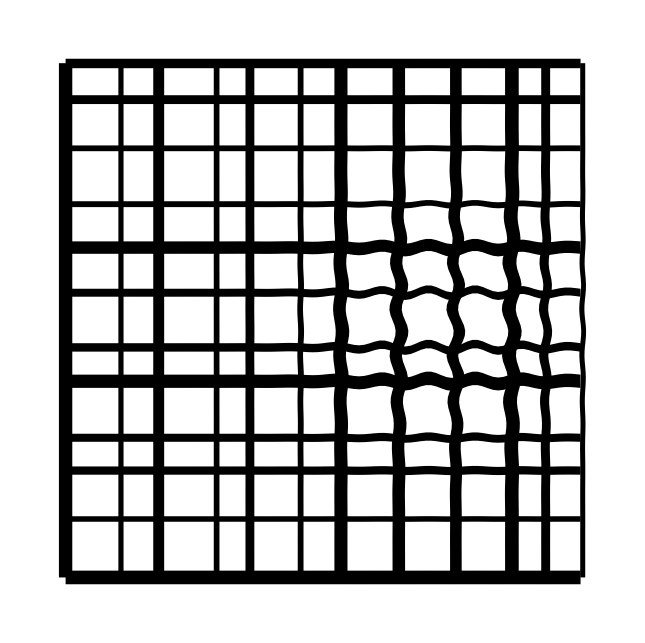

```mathematica
Graphics[Map[Polygon,gridMATLAB]]
```

### színhatások táblázat

#### fonódó

```mathematica
n=3;
res=100;
zAmp=0.1;
pointsX=Table[Table[
{k ,j  2Pi,If[Mod[j,2]==0,zAmp Sin[k],zAmp Cos[k]]}
,{k,0,n 3Pi/2,n 3Pi/2/res}],{j,0,n-1}];
pointsY=Table[Table[
{j 2Pi,k,If[Mod[j,2]==0,zAmp Sin[k],zAmp Cos[k]]}
,{k,0,n 3Pi/2,n 3Pi/2/res}],{j,0,n-1}];
Show[{
ListPlot3D[{{0,0,0},{0,0,0}},AspectRatio->1],
Graphics3D[{
Green,Map[Line,pointsX],
Red,Map[Line,pointsY]
}]
}]
```

-Graphics3D-

#### szín cikk replikáció

```mathematica
n=6;
res=100;
r=0.25;

sNL=0;
bNL=0;

sC={0.5,0.5};
sL=2;
sS=10;
sA=0;

scintillation=False;

aperture = True;

aC={0.5,0.5};
aW=1.1;
aO = 0.85;

hTilt=0;
vTilt =0;

sW=(r/(1+r))(1/n);
bW=(1/(1+r)) (1/n);
sNH=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];
bNH=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];
sNV=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];
bNV=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];

aperturePoints=Map[
aC+ aW #&,
Join[
Table[(aO/2){Cos[k],Sin[k]},{k,0,2Pi,Pi/100}],
{{0.5,0},{0.5,-0.5},{-0.5,-0.5},{-0.5,0.5},{0.5,0.5},{0.5,0},{0.5,0}}
]
];

hCoords=Table[
(sW Total[sNH[[1;;i-1]]]+bW Total[bNH[[1;;i-1]]]+sW(sNH[[i]]-sNH[[1]])/2)/
(sW Total[sNH]+bW Total[bNH]-sW(sNH[[1]]+sNH[[n]])/2)
,{i,1,n+1}];
vCoords=Table[
(sW Total[sNV[[1;;i-1]]]+bW Total[bNV[[1;;i-1]]]+sW(sNV[[i]]-sNV[[1]])/2)/
(sW Total[sNV]+bW Total[bNV]-sW(sNV[[1]]+sNV[[n]])/2)
,{i,1,n+1}];

verticalStreets=Table[
Map[#+{hCoords[[i]],0.5}&,Transpose[RotationMatrix[hTilt].Transpose[Map[#-{hCoords[[i]],0.5}&,Join[
Table[
{
hCoords[[i]]+0.5sW sNH[[i]]+
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{hCoords[[i]]+0.5sW sNH[[i]],k}]-sL)])),
k
}
,{k,0,1,1/res}],
Reverse[Table[
{
hCoords[[i]]-0.5sW sNH[[i]]+
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{hCoords[[i]]-0.5sW sNH[[i]],k}]-sL)])),
k
}
,{k,0,1,1/res}]]
]]]]],
{i,1,n+1}] ;

horizontalStreets=
Table[
Map[#+{0.5,vCoords[[i]]}&,Transpose[RotationMatrix[vTilt].Transpose[Map[#-{0.5,vCoords[[i]]}&,Join[
Table[
{
k,
vCoords[[i]]+0.5sW sNV[[i]]-
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{k,vCoords[[i]]+0.5sW sNV[[i]]}]-sL)]))
}
,{k,0,1,1/res}],
Reverse[Table[
{
k,
vCoords[[i]]-0.5sW sNV[[i]]-
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{k,vCoords[[i]]-0.5sW sNV[[i]]}]-sL)]))
}
,{k,0,1,1/res}]]
]]]]],
{i,1,n+1}];

gridPoints=Join[horizontalStreets,verticalStreets];
```

- hue ugyanaz, value (brightness) ugyanaz, chroma (saturation) különböző
-Graphics-
- ahogy a háttér egyre szaturáltabb az alsó sávhoz képest, úgy a foltok egyre világosabbnak látszanak a kereszteződésnél
- ahogy a háttér egyre kevésbé szaturáltabb az alsó sávhoz képest, úgy a foltok egyre sötétebbnek látszanak a kereszteződésnél
- ez a háttér alap szaturáltságától független
- mennyire szabad változó a két sáv szaturációs különbsége?

-Graphics-
- ahogy a háttér egyre kevésbé szaturáltabb a felső sávnál, úgy egyre világosabbnak tűnnek a foltok a kereszteződésnél
- ez függ a háttér alap szaturáltságánál, minél szaturáltabb, annál erősebben jelentkezik
- mennyire szabad változó a két sáv szaturációs különbsége?

-Graphics-
- ahogy a háttér egyre kevésbé szaturáltabb a felső sávnál, úgy egyre sötétebbnek tűnnek a foltok a kereszteződésnél
- ez függ a háttér alap szaturáltságánál, minél szaturáltabb, annál erősebben jelentkezik
- mennyire szabad változó a két sáv szaturációs különbsége?

```mathematica
Manipulate[
{
eset=Transpose[ArrayReshape[Join[
{
Graphics[{FontFamily->"Cambria",FontSize->18,
Text[
"number of blocks = "<>ToString[n]<>", street/block ratio = "<>ToString[r]<>"\nstreet noise = ±"<>ToString[sNL]<>", block noise = ±"<>ToString[bNL]<>", "<>"\nsine amplitude = "<>ToString[sA]<>", sine cutoff = "<>If[sA==0||1<sL,"0",ToString[sS]]
,{0.5,1.075}]
},ImageSize->{700,100},AspectRatio->0.025],
Graphics[ImageSize->{700,100},AspectRatio->0.025]
},
Table[
Graphics[{
Hue[hue,blockSaturation,brightness],EdgeForm[Gray],Rectangle[{0,0},{1,1}],
EdgeForm[None],
If[
scintillation,
{
RGBColor[0.5,0.5,0.5,1],Map[Polygon,gridPoints],
RGBColor[1,1,1],Table[Table[
Ellipsoid[{hCoords[[i]],vCoords[[j]]},0.5{sW sNH[[i]],sW sNV[[j]]}]
,{j,1,n+1}],{i,1,n+1}]
},
If[
vOnH,
{
Hue[hue,lowerSautration,brightness,1],Map[Polygon,horizontalStreets],
Hue[hue,upperSaturation,brightness,1],Map[Polygon,verticalStreets]
},
{
Hue[hue,lowerSautration,brightness,1],Map[Polygon,verticalStreets],
Hue[hue,upperSaturation,brightness,1],Map[Polygon,horizontalStreets]
}
]
],
If[
aperture,
{
RGBColor[0.5,0.5,0.5,1],Polygon[aperturePoints]
}
]
},ImageSize->{700,700},AspectRatio->1],{scintillation,{False,True}}]
],{2,2}]][[1]][[2]],

If[export,
{Export["Y:\\Beno\\hermann_grid\\presentations\\colors cikk\\blockSat_"<>ToString[blockSaturation]<>"_lowSat_"<>ToString[lowerSautration]<>"_upSat_"<>ToString[upperSaturation]<>".png",eset],export=False}
]
},

{{hue,1},0,1,0.0001},
{{brightness,1},0,1,0.05},

{{blockSaturation,0.25},0,1,0.05},
{{lowerSautration,1},0,1,0.05},
{{upperSaturation,0.75},0,1,0.05},

{{vOnH,True},{False,True}},
{{export,False},{False,True}}
]
```

StringJoin::string: String expected at position 2 in number of blocks = 5, street/block ratio = 0.25
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Part::partd: Part specification hCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification vCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification sNH⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in number of blocks = 5, street/block ratio = 0.1
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Part::partd: Part specification hCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification vCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification sNH⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in number of blocks = 5, street/block ratio = 0.5
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Part::partd: Part specification hCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification vCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification sNH⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = 2, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Part::partd: Part specification hCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification vCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification sNH⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in number of blocks = 2, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Part::partd: Part specification hCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification vCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification sNH⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = 4, street/block ratio = 1
-
4
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Part::partd: Part specification hCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification vCoords⟦1⟧ is longer than depth of object.

Part::partd: Part specification sNH⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

StringJoin::string: String expected at position 2 in number of blocks = n, street/block ratio = r
street noise = ±sNL, block noise = ±bNL, 
sine amplitude = sA, sine cutoff = <>If[sA==0||1<sL,0,ToString[sS]].

Table::iterb: Iterator {i,1,1+n} does not have appropriate bounds.

### Murray cikk

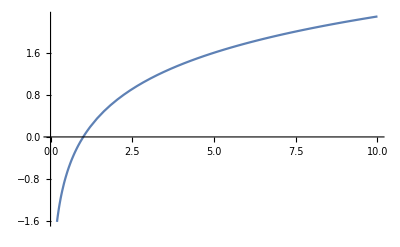

```mathematica
Plot[Log[x],{x,0,10}]
```

```mathematica
illusion={{35,35,70,35,35,35,35,35,70,35,35,35,70,35,35,35},{35,35,35,17.5000000000000,35,35,35,17.5000000000000,35,35,25,35,35,17.5000000000000,35,35},{35,35,70,35,35,25,35,35,70,35,35,35,70,35,35,35},{35,35,35,17.5000000000000,35,35,35,17.5000000000000,35,35,49,35,35,17.5000000000000,35,35},{35,35,70,35,35,49,35,35,70,35,35,35,70,35,35,35},{35,35,35,17.5000000000000,35,35,35,17.5000000000000,35,35,25,35,35,17.5000000000000,35,35},{35,35,70,35,35,25,35,35,70,35,35,35,70,35,35,35},{35,35,35,17.5000000000000,35,35,35,17.5000000000000,35,35,49,35,35,17.5000000000000,35,35},{35,35,70,35,35,49,35,35,70,35,35,35,70,35,35,35},{35,35,35,17.5000000000000,35,35,35,17.5000000000000,35,35,25,35,35,17.5000000000000,35,35},{35,35,70,35,35,25,35,35,70,35,35,35,70,35,35,35},{35,35,35,17.5000000000000,35,35,35,17.5000000000000,35,35,49,35,35,17.5000000000000,35,35},{35,35,70,35,35,49,35,35,70,35,35,35,70,35,35,35},{35,35,35,17.5000000000000,35,35,35,17.5000000000000,35,35,25,35,35,17.5000000000000,35,35},{35,35,70,35,35,25,35,35,70,35,35,35,70,35,35,35},{35,35,35,17.5000000000000,35,35,35,17.5000000000000,35,35,35,35,35,17.5000000000000,35,35}};
```

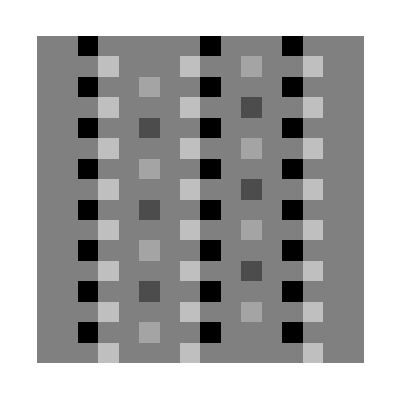

```mathematica
ArrayPlot[illusion]
```

```mathematica
hermannPng=Import["Y:\\Beno\\hermann_grid\\lit\\Murray_supporting_information\\hermann_grid_1.png"];
```

```mathematica
hermannData=ImageData[hermannPng]/.{{0.,0.,0.}->0,{1.,1.,1.}->1}
```

{{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0},{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0}}

```mathematica
MEvaluate["load('Y:/Beno/hermann_grid/lit/Murray_supporting_information/code/tools/grid_stimuli.mat')"]
```

```mathematica
MEvaluate["who"]
```

Your variables are:

argyle              checkassim          koffka_broken       snake               
argyle2             hermann1            koffka_connected    snake_control       
argyle_control      hermann2            simcon              white               
argyle_long         koffka_adelson      simcon_articulated

```mathematica
Export["Y:\\Beno\\hermann_grid\\presentations\\murray_jov_labmeeting\\simconart.png",ArrayPlot["imL"/.MGet["simcon_articulated"]]]
```

Y:\Beno\hermann_grid\presentations\murray_jov_labmeeting\simconart.png

```mathematica
MSet[
"hermann1",
{"imL"->hermannData1,"test1"->{9.,11.,9.,11.},"test2"->{10.,6.,10.,6.}}
]
```

```mathematica
MSet[
"hermann2",
{"imL"->hermannData2,"test1"->{9.,11.,9.,11.},"test2"->{10.,6.,10.,6.}}
]
```

```mathematica
MEvaluate["save('Y:/Beno/hermann_grid/lit/Murray_supporting_information/code/tools/grid_stimuli.mat')"]
```

```mathematica
hermannData//Dimensions
```

{16,16}

```mathematica
hermannData1=hermannData 70;
```

```mathematica
hermannData2=70 hermannData/.{1->0,0->1};
```

```mathematica
hermannData1
```

{{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0},{0,70,0,0,0,70,0,0,0,70,0,0,0,70,0,0}}

```mathematica
DrawGrid3D[from_,to_,translate_]:={
Table[Line[{{i,from[[2]],0}+translate,{i,to[[2]],0}+translate}],{i,from[[1]],to[[1]]}],
Table[Line[{{from[[1]],i,0}+translate,{to[[1]],i,0}+translate}],{i,from[[2]],to[[2]]}]
}
```

```mathematica
jovExport=Graphics3D[{
Thickness[0.005],Dotted,
DrawGrid3D[{0,0},{5,5},{0,0,0}],
DrawGrid3D[{0,0},{5,5},{0,0,-4}],
Dashing->None,
DrawGrid3D[{1,1},{4,4},{0,0,0}],
DrawGrid3D[{1,1},{4,4},{0,0,-4}],
PointSize[0.025],Red,Point[{2.5,2.5,0}],
Dashing->None,Thickness[0.0025],Red,
Line[{{2.5,2.5,0},{2.5,2.5,-4}}],
Table[Line[{{2.5,2.5,0},{2.5,2.5,0}+{Cos[r],Sin[r],0}}],{r,0,2Pi,Pi/2}],
Table[Line[{{2.5,2.5,0},{2.5,2.5,0}+Sqrt[2]{Cos[r],Sin[r],0}}],{r,Pi/4,2Pi,Pi/2}],
Table[Line[{{2.5,2.5,0},{2.5,2.5,-4}+{Cos[r],Sin[r],0}}],{r,0,2Pi,Pi/2}],
Table[Line[{{2.5,2.5,0},{2.5,2.5,-4}+Sqrt[2]{Cos[r],Sin[r],0}}],{r,Pi/4,2Pi,Pi/2}]
},Boxed->False]
```

-Graphics3D-

```mathematica
Export["Y:\\Beno\\hermann_grid\\presentations\\murray_jov_labmeeting\\jov_3.png",-Graphics3D-]
```

Y:\Beno\hermann_grid\presentations\murray_jov_labmeeting\jov_3.png

```mathematica
Twist[mat_]:=(Log[mat[[1]][[1]]]-Log[mat[[2]][[1]]])-(Log[mat[[1]][[2]]]-Log[mat[[2]][[2]]])
```

```mathematica
Twist[{
{10,1},
{1,1}
}]
```

Log[10]

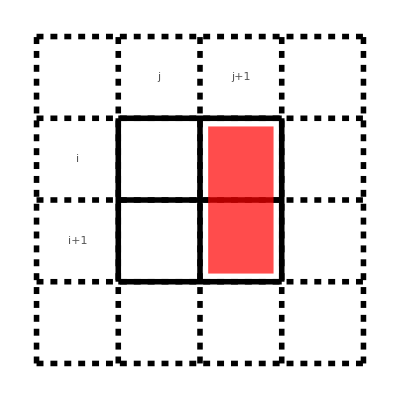

```mathematica
jovExport2=Graphics[{
Thickness->0.01,
Black,
Dashed,
Table[{
Line[{{0,i},{4,i}}],
Line[{{i,0},{i,4}}]
},{i,0,4}],
Dashing->None,
Table[{
Line[{{1,i},{3,i}}],
Line[{{i,1},{i,3}}]
},{i,1,3}],
FontFamily->"Garamond",FontSize->42,Darker[Gray],
Style[Text["i",{0.5,2.5}],Italic],
Style[Text["i+1",{0.5,1.5}],Italic],
Style[Text["j",{1.5,3.5}],Italic],
Style[Text["j+1",{2.5,3.5}],Italic],
RGBColor[1,0,0,0.7],
Rectangle[{2.1,1.1},{2.9,2.9}]
}]
```

```mathematica
Export["Y:\\Beno\\hermann_grid\\presentations\\murray_jov_labmeeting\\jov2_7.png",jovExport2]
```

Y:\Beno\hermann_grid\presentations\murray_jov_labmeeting\jov2_7.png

```mathematica
Twist[{

}]
```

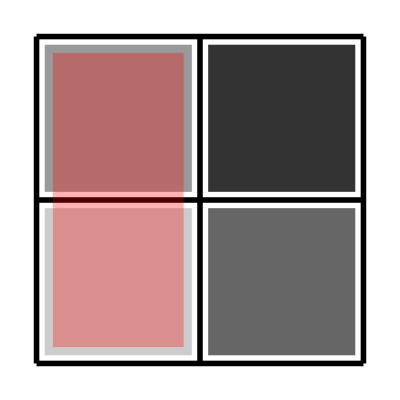

```mathematica
jovExport3=Graphics[{
Thickness->0.01,
Black,
Table[{
Line[{{0,i},{2,i}}],
Line[{{i,0},{i,2}}]
},{i,0,2}],
RGBColor[0,0,0,0.2],Rectangle[{0.05,0.05},{0.95,0.95}],
RGBColor[0,0,0,0.4],Rectangle[{0.05,1.05},{0.95,1.95}],
RGBColor[0,0,0,0.6],Rectangle[{1.05,0.05},{1.95,0.95}],
RGBColor[0,0,0,0.8],Rectangle[{1.05,1.05},{1.95,1.95}],
RGBColor[1,0,0,0.3],Rectangle[{0.1,0.1},{0.9,1.9}]
}]
```

```mathematica
Export["Y:\\Beno\\hermann_grid\\presentations\\murray_jov_labmeeting\\jov4_1.png",jovExport3]
```

Y:\Beno\hermann_grid\presentations\murray_jov_labmeeting\jov4_1.png

```mathematica
Twist[{
{1,1},
{2,1}
}]//N
```

-0.693147

```mathematica
Plot[Log[x],{x,0,10}]
```

-Graphics-

### McCollough - Hermann interakció

```mathematica
n=6;
res=100;
r=0.25;

sNL=0;
bNL=0;

sC={0.5,0.5};
sL=2;
sS=10;
sA=0;

scintillation=False;

aperture = True;

aC={0.5,0.5};
aW=1.1;
aO = 0.85;

hTilt=0;
vTilt =0;

sW=(r/(1+r))(1/n);
bW=(1/(1+r)) (1/n);
sNH=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];
bNH=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];
sNV=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];
bNV=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];

aperturePoints=Map[
aC+ aW #&,
Join[
Table[(aO/2){Cos[k],Sin[k]},{k,0,2Pi,Pi/100}],
{{0.5,0},{0.5,-0.5},{-0.5,-0.5},{-0.5,0.5},{0.5,0.5},{0.5,0},{0.5,0}}
]
];

hCoords=Table[
(sW Total[sNH[[1;;i-1]]]+bW Total[bNH[[1;;i-1]]]+sW(sNH[[i]]-sNH[[1]])/2)/
(sW Total[sNH]+bW Total[bNH]-sW(sNH[[1]]+sNH[[n]])/2)
,{i,1,n+1}];
vCoords=Table[
(sW Total[sNV[[1;;i-1]]]+bW Total[bNV[[1;;i-1]]]+sW(sNV[[i]]-sNV[[1]])/2)/
(sW Total[sNV]+bW Total[bNV]-sW(sNV[[1]]+sNV[[n]])/2)
,{i,1,n+1}];

verticalStreets=Table[
Map[#+{hCoords[[i]],0.5}&,Transpose[RotationMatrix[hTilt].Transpose[Map[#-{hCoords[[i]],0.5}&,Join[
Table[
{
hCoords[[i]]+0.5sW sNH[[i]]+
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{hCoords[[i]]+0.5sW sNH[[i]],k}]-sL)])),
k
}
,{k,0,1,1/res}],
Reverse[Table[
{
hCoords[[i]]-0.5sW sNH[[i]]+
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{hCoords[[i]]-0.5sW sNH[[i]],k}]-sL)])),
k
}
,{k,0,1,1/res}]]
]]]]],
{i,1,n+1}] ;

horizontalStreets=
Table[
Map[#+{0.5,vCoords[[i]]}&,Transpose[RotationMatrix[vTilt].Transpose[Map[#-{0.5,vCoords[[i]]}&,Join[
Table[
{
k,
vCoords[[i]]+0.5sW sNV[[i]]-
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{k,vCoords[[i]]+0.5sW sNV[[i]]}]-sL)]))
}
,{k,0,1,1/res}],
Reverse[Table[
{
k,
vCoords[[i]]-0.5sW sNV[[i]]-
sA bW Sin[2 Pi k n](1/(1+Exp[sS (2EuclideanDistance[sC,{k,vCoords[[i]]-0.5sW sNV[[i]]}]-sL)]))
}
,{k,0,1,1/res}]]
]]]]],
{i,1,n+1}];

gridPoints=Join[horizontalStreets,verticalStreets];
```

```mathematica
Manipulate[
Graphics[{
Hue[col,1,1],Rectangle[{0,0},{1,1}],
Hue[FractionalPart[0.5+col],1,1],Rectangle[{1,0},{2,1}]
}]
,{{col,0.5},0,1}]
```

```mathematica
Manipulate[
{
Graphics[{
Hue[hue,blockSaturation,blockBrightness],EdgeForm[Gray],Rectangle[{0,0},{1,1}],
EdgeForm[None],
If[
scintillation,
{
RGBColor[0.5,0.5,0.5,1],Map[Polygon,gridPoints],
RGBColor[1,1,1],Table[Table[
Ellipsoid[{hCoords[[i]],vCoords[[j]]},0.5{sW sNH[[i]],sW sNV[[j]]}]
,{j,1,n+1}],{i,1,n+1}]
},
If[
mcc,
{
Hue[FractionalPart[0.5+hue],lowerSautration,streetBrightness],Rectangle[{0,0},{1,1}],
Black,Table[
Rectangle[
{i 1/(2m+1),0},
{(i+1)1/(2m+1),1}
]
,{i,0,2m+1,2}]
},
If[
vOnH,
{
Hue[hue,lowerSautration,streetBrightness,1],Map[Polygon,horizontalStreets],
Hue[hue,upperSaturation,streetBrightness,1],Map[Polygon,verticalStreets]
},
{
Hue[hue,lowerSautration,streetBrightness,1],Map[Polygon,verticalStreets],
Hue[hue,upperSaturation,streetBrightness,1],Map[Polygon,horizontalStreets]
}
]
]
],
If[
aperture,
{
RGBColor[0.5,0.5,0.5,1],Polygon[aperturePoints]
}
]
},ImageSize->{700,700},AspectRatio->1],

(*If[export,
{Export["Y:\\Beno\\hermann_grid\\hermann_mccollough\\"<>ToString[Input["fájl neve?"]]<>"_"<>ToString[blockSaturation]<>"_lowSat_"<>ToString[lowerSautration]<>"_upSat_"<>ToString[upperSaturation]<>".png",eset],export=False}
]*)
},

{{m,2n},1,20,1},
{{hue,0},0,1,0.1},
{{blockBrightness,0},0,1,0.05},
{{streetBrightness,1},0,1,0.05},

{{blockSaturation,1},0,1,0.05},
{{lowerSautration,0.8},0,1,0.05},
{{upperSaturation,0.8},0,1,0.05},

{{vOnH,True},{False,True}},
{{export,False},{False,True}},
{{aperture,False},{False,True}},
{{mcc,True},{False,True}}
]
```

```mathematica
m=2n;
blockBrightness=0;
streetBrightness=1;
blockSaturation=1;
streetSaturation=0.6;
aperture=False;
Table[Table[Table[{
Export[
If[
mcc,
If[
horizontalMcc,
"Y:\\Beno\\hermann_grid\\hermann_mccollough\\1_horizontal_1_mcc_hue_"<>ToString[FractionalPart[0.5+hue]],
"Y:\\Beno\\hermann_grid\\hermann_mccollough\\2_vertical_1_mcc_hue_"<>ToString[FractionalPart[0.5+hue]]
],
If[
horizontalMcc,
"Y:\\Beno\\hermann_grid\\hermann_mccollough\\1_horizontal_2_hermann_hue_"<>ToString[hue],
"Y:\\Beno\\hermann_grid\\hermann_mccollough\\2_vertical_2_hermann_hue_"<>ToString[hue]
]
],
Graphics[{
Hue[hue,blockSaturation,blockBrightness],EdgeForm[Gray],Rectangle[{0,0},{1,1}],
EdgeForm[None],
If[
mcc,
{
Hue[FractionalPart[0.5+hue],lowerSautration,streetBrightness],Rectangle[{0,0},{1,1}],
Black,
If[
horizontalMcc,
Table[
Rectangle[
{0,i 1/(2m+1)},
{1,(i+1)1/(2m+1)}
]
,{i,0,2m+1,2}],
Table[
Rectangle[
{i 1/(2m+1),0},
{(i+1)1/(2m+1),1}
]
,{i,0,2m+1,2}]
]
},
{
Hue[hue,streetSaturation,streetBrightness,1],Map[Polygon,horizontalStreets],
Hue[hue,streetSaturation,streetBrightness,1],Map[Polygon,verticalStreets]
}
]
,
If[aperture,{RGBColor[0.5,0.5,0.5,1],Polygon[aperturePoints]}]
},ImageSize->{700,700},AspectRatio->1]];
(*If[export,
{Export["Y:\\Beno\\hermann_grid\\hermann_mccollough\\"<>ToString[Input["fájl neve?"]]<>"_"<>ToString[blockSaturation]<>"_lowSat_"<>ToString[lowerSautration]<>"_upSat_"<>ToString[upperSaturation]<>".png",eset],export=False}
]*)
},{mcc,{False,True}}],{hue,0,1,0.1}],{horizontalMcc,{True,False}}]
```

### raszteres

```mathematica
MinPos[list_]:=Flatten[Position[list,Min[list]]][[1]]
```

```mathematica
sW//N
```

0.047619

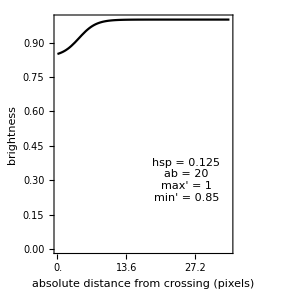
-Graphics--Graphics--Graphics-

```mathematica
n=4;
r=1/4;
approxSize=200;

hsp=0.125;
ab=20;
min=0;
max=0.15;

bW=1/(n+r+n r);
sW=r bW;
coords=Table[0.5sW+(i-1)(sW+bW),{i,1,n+1}];

possibleSizes=DeleteCases[
Table[
If[(n+1)Round[sW pixelSize]+n Round[bW pixelSize]==pixelSize,pixelSize]
,{pixelSize,approxSize-2n,approxSize+2n}]
,Null];

pixelSize=possibleSizes[[MinPos[
Map[
Abs[approxSize-#]&,
possibleSizes
]]]];

pixelCoords =Flatten[ Table[Table[
If[i==3&&j==3,
{-100,-100},
{Round[coords[[i]] pixelSize,0.5],Round[coords[[j]] pixelSize,0.5]}
]
,{j,2,n}],{i,2,n}],1];

maxPossibleDistance=Sqrt[2Power[pixelSize(sW+bW)/2,2]];

gridMatrix1=Table[Table[
If[
Total[Table[If[Abs[i pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ||
Total[Table[If[Abs[j pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ,
1,
0
]
,{j,1/pixelSize,1,1/pixelSize}],{i,1/pixelSize,1,1/pixelSize}];
gridMatrix2=Table[Table[
If[
Total[Table[If[Abs[i pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ||
Total[Table[If[Abs[j pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ,
If[
DistFunction[{i pixelSize-0.5,j pixelSize-0.5}]≤maxPossibleDistance,
If[
DistFunction[{i pixelSize-0.5,j pixelSize-0.5}]≤ sW pixelSize 0.5 10 ,
IllusionFunction[
DistFunction[{i pixelSize-0.5,j pixelSize-0.5}]/maxPossibleDistance,
hsp,
ab,
min,
max
],
1
],
1
],
0
]
,{j,1/pixelSize,1,1/pixelSize}],{i,1/pixelSize,1,1/pixelSize}]; 
imSize=300;
gridImage=Row[{
Image[gridMatrix1,ImageSize->{imSize,imSize}],
Plot[
IllusionFunction[d,hsp,ab,min,max],{d,0,1},
PlotStyle->{Black,Thick},PlotRange->{{0,1},{0,1}},
LabelStyle->{Black,FontFamily->"Cambria",FontSize->14},
Frame->{{True,False},{True,True}},
FrameLabel->{{"brightness",None},{"absolute distance from crossing (pixels)","relative distance from crossing"}},
FrameTicks->{{Automatic,None},{Table[{i,NumberForm[i maxPossibleDistance,3]},{i,0,1,0.2}],Table[i,{i,0,1,0.2}]}},
Epilog->{
Black,FontFamily->"Cambria",FontSize->20,Text["hsp = "<>ToString[hsp]<>"\nab = "<>ToString[ab]<>"\nmax' = "<>ToString[1-min]<>"\nmin' = "<>ToString[1-max],{0.75,0.3}](*,
RGBColor[1,1,1,0.8],
EdgeForm[Black],
Rectangle[{0.1,0.2},{0.98,0.8}],
RGBColor[1,0,0,1],FontSize->60,Text["TraditionalForm`r",{0.55,0.5}]*)},
AspectRatio->1,ImageSize->{imSize,imSize}
],
Image[gridMatrix2,ImageSize->{imSize,imSize}]
}]
```

```mathematica
Export["Y:\\Beno\\hermann_grid\\grids\\v2\\n_"<>ToString[n]<>"_ab_"<>ToString[ab]<>"_hsp_"<>ToString[hsp]<>"_min_"<>ToString[1-max]<>".png",gridImage];
```

```mathematica
Export["Y:\\Beno\\hermann_grid\\grids\\r_limit.png",gridImage];
```

```mathematica
Clear[r,sW]
```

```mathematica
r≤sW/2//TraditionalForm
```

r≤sW/2

```mathematica
DistFunction[pos_]:=Min[Map[EuclideanDistance[pos,#]&,pixelCoords]]
```

```mathematica
IllusionFunction[d_,hsp_,ab_,min_,max_]:=1-G[d,hsp,ab,min,max]
```

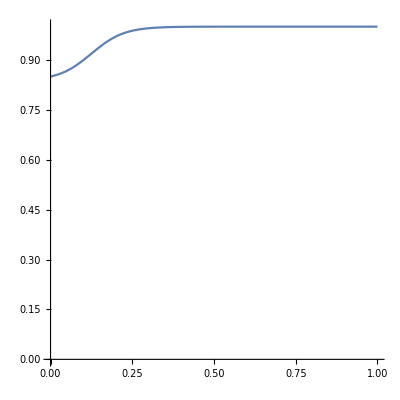

```mathematica
hsp=0.125;
ab=20;
min=0;
max=0.15;
Plot[
IllusionFunction[d,hsp,ab,min,max],
{d,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1
]
```

```mathematica
IllusionFunction[d,hsp,ab,min,max]//TraditionalForm
```

-((max-min) (1/(ⅇ^(ab (d-hsp))+1)-1/(ⅇ^(ab (1-hsp))+1)))/(1/(ⅇ^(-ab hsp)+1)-1/(ⅇ^(ab (1-hsp))+1))-min+1

```mathematica
F[d_,hsp_,ab_]:=1/(1+Exp[ ab(d- hsp)])
```

```mathematica
G[d_,hsp_,ab_,min_,max_]:=(F[d,hsp,ab]-F[1,hsp,ab])(max-min)/(F[0,hsp,ab]-F[1,hsp,ab])+min
```

```mathematica
G2[F_,dist_,min_,max_]:=(F[dist]-F[1])(max-min)/(F[0]-F[1])+min
```

```mathematica
Clear[hsp,ab,min,max]
```

```mathematica
G2[f,dist,min,max]//TraditionalForm
```

((f(dist)-f(1)) (max-min))/(f(0)-f(1))+min

```mathematica
F[dist,hsp,ab]//TraditionalForm
```

1/(ⅇ^(ab (dist-hsp))+1)

```mathematica
MEvaluate["addpath('Y:/Beno/hermann_grid')"];
```

```mathematica
MEvaluate["gridMatrix = generateRasterGrid(5, 1/4, 200);"]
Image[MGet["gridMatrix"]]
```

-Graphics-

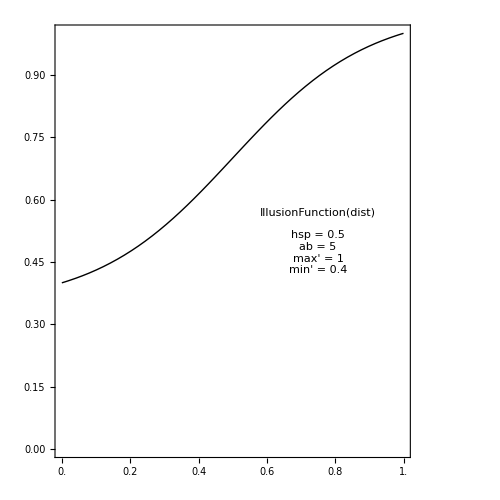

```mathematica
hsp=0.5;
ab=5;
min=0;
max=0.6;
iPlot=Plot[
1-G[d,hsp,ab,min,max],{d,0,1},
PlotStyle->{Black,Thick},PlotRange->{{0,1},{0,1}},
LabelStyle->{Black,FontFamily->"Cambria",FontSize->14},
Frame->{True,True},
FrameTicks->{{Automatic,None},{Table[i,{i,0,1,0.2}],None}},
Epilog->{Black,FontFamily->"Cambria",FontSize->20,Text["IllusionFunction(dist)\n\nhsp = "<>ToString[hsp]<>"\nab = "<>ToString[ab]<>"\nmax' = "<>ToString[1-min]<>"\nmin' = "<>ToString[1-max],{0.75,0.5}]},
AspectRatio->1,ImageSize->{500,500}
]
```

```mathematica
Export["Y:\\Beno\\hermann_grid\\presentations\\v2\\iPlot.png",iPlot];
```